```mathematica
(* Gaussian sensing: Kitaev chain*)

(*a1,a2,...,an,a1d,...and -> x1,x2...,xn,p1,...pn*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]
```

```mathematica
Clear[g,χ]
Nmodes=2;
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
λ=Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{FcovEP,nEP}={1/4 Tr[Inverse[Σin].D[Σin,χ].Inverse[Σin].D[Σin,χ]]//FullSimplify,1/2 (Tr[Σin]-2 Nmodes)}
```

{4 t^2,4 t^2 χ^2}

```mathematica
Clear[χ,g]
Nmodes=2;
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{Fcov,n}={1/4 Tr[Inverse[Σin].D[Σin,χ].Inverse[Σin].D[Σin,χ]]//FullSimplify,1/2 (Tr[Σin]-2 Nmodes)//FullSimplify}
Assuming[g>χ,FullSimplify[Fcov/n]]
Assuming[g<χ,FullSimplify[Fcov/n]]
```

{1/(2 (g^2-χ^2)^3)(4 g^4-8 t^2 χ^6+g^2 χ^2 (-3+8 t^2 χ^2)+g^2 (4 (-g^2+χ^2) Cosh[2 t √(-g^2+χ^2)]-χ^2 (Cosh[4 t √(-g^2+χ^2)]-8 t √(-g^2+χ^2) Sinh[2 t √(-g^2+χ^2)]))),(4 χ^2 Sinh[t √(-g^2+χ^2)]^2)/(-g^2+χ^2)}

1/(8 (-g^2 χ+χ^3)^2)Csch[t √(-g^2+χ^2)]^2 (-4 g^4+8 t^2 χ^6+g^2 χ^2 (3-8 t^2 χ^2)+g^2 (4 (g-χ) (g+χ) Cos[2 t √(g^2-χ^2)]+χ^2 (Cos[4 t √(g^2-χ^2)]+8 t √((g-χ) (g+χ)) Sin[2 t √(g^2-χ^2)])))

1/(8 (-g^2 χ+χ^3)^2)Csch[t √(-g^2+χ^2)]^2 (-4 g^4+8 t^2 χ^6+g^2 χ^2 (3-8 t^2 χ^2)+g^2 (4 (g-χ) (g+χ) Cosh[2 t √(-g^2+χ^2)]+χ^2 (Cosh[4 t √(-g^2+χ^2)]-8 t √(-g^2+χ^2) Sinh[2 t √(-g^2+χ^2)])))

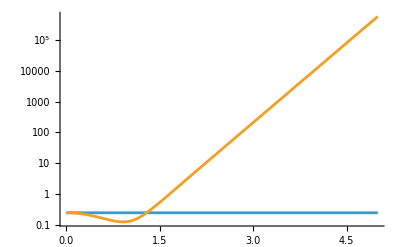

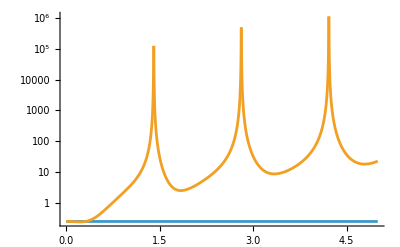

```mathematica
χ=2;g=.3;
LogPlot[{FcovEP/nEP,Fcov/n},{t,0,5}]
χ=2;g=3;
LogPlot[{FcovEP/nEP,Fcov/n},{t,0,5}]
```

```mathematica
Clear[g,χ]
Nmodes=2;
EOM={{-I ω1,g,ξ1,χ},{-g,-I ω2,χ,ξ2},{ξ1,χ,I ω1,g},{χ,ξ2,-g,I ω2}}/.{ξ2->0,ω2->0,ω1->0,ξ1->2 g,χ->0};
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{FcovEP,nEP}={1/4 Tr[Inverse[Σin].D[Σin,g].Inverse[Σin].D[Σin,g]]//FullSimplify,1/2 (Tr[Σin]-2 Nmodes)//FullSimplify}
```

{8 t^2,-2+(2+4 g^2 t^2) Cosh[2 g t]}

```mathematica
Clear[g,χ]
Nmodes=2;
EOM={{-I ω1,g,ξ1,χ},{-g,-I ω2,χ,ξ2},{ξ1,χ,I ω1,g},{χ,ξ2,-g,I ω2}}/.{ξ2->0,ω2->0,ω1->0,χ->0};
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{Fcov,n}={1/4 Tr[Inverse[Σin].D[Σin,g].Inverse[Σin].D[Σin,g]]//FullSimplify,1/2 (Tr[Σin]-2 Nmodes)//FullSimplify}
```

{1/((-4 g^2+ξ1^2)^3)2 ξ1^2 (3 ξ1^2+8 g^2 (-2+t^2 (-4 g^2+ξ1^2))+4 (4 g^2-ξ1^2) Cosh[t √(-4 g^2+ξ1^2)]+ξ1^2 Cosh[2 t √(-4 g^2+ξ1^2)]-16 g^2 t √(-4 g^2+ξ1^2) Sinh[t √(-4 g^2+ξ1^2)]),-2+(2 Cosh[t ξ1] (4 g^2-ξ1^2 Cosh[t √(-4 g^2+ξ1^2)]))/(4 g^2-ξ1^2)}

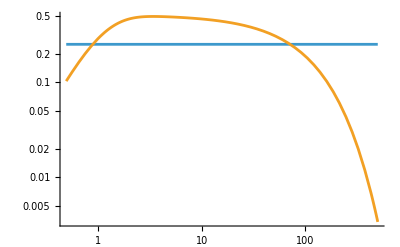

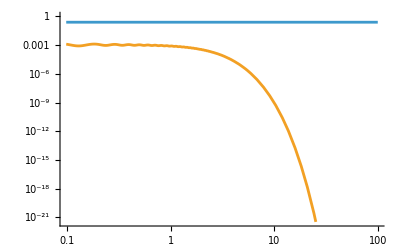

```mathematica
ξ1=2;g=.1;
LogLogPlot[{FcovEP/nEP,Fcov/n},{t,0,500},PlotRange->All]
χ=ξ1;g=30;
LogLogPlot[{FcovEP/nEP,Fcov/n},{t,0,100}]
t=5;
```

```mathematica
Clear[ξ1,g]
EOM//Eigensystem
```

{{1/2 (-ξ1-√(-4 g^2+ξ1^2)),1/2 (ξ1-√(-4 g^2+ξ1^2)),1/2 (-ξ1+√(-4 g^2+ξ1^2)),1/2 (ξ1+√(-4 g^2+ξ1^2))},{{-(ξ1+√(-4 g^2+ξ1^2))/(2 g),-1,-(-ξ1-√(-4 g^2+ξ1^2))/(2 g),1},{-(ξ1-√(-4 g^2+ξ1^2))/(2 g),1,-(ξ1-√(-4 g^2+ξ1^2))/(2 g),1},{-(ξ1-√(-4 g^2+ξ1^2))/(2 g),-1,-(-ξ1+√(-4 g^2+ξ1^2))/(2 g),1},{-(ξ1+√(-4 g^2+ξ1^2))/(2 g),1,-(ξ1+√(-4 g^2+ξ1^2))/(2 g),1}}}

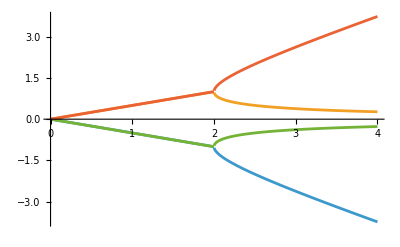

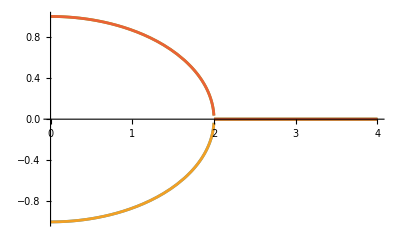

```mathematica
λ1=1/2 (-ξ1g-√(-4+ξ1g^2));
λ2=1/2 (ξ1g-√(-4+ξ1g^2));
λ3=1/2 (-ξ1g+√(-4+ξ1g^2));
λ4=1/2 (ξ1g+√(-4+ξ1g^2));
Plot[{Re[λ1],Re[λ2],Re[λ3],Re[λ4]},{ξ1g,0,4}]
Plot[{Im[λ1],Im[λ2],Im[λ3],Im[λ4]},{ξ1g,0,4}]
```